```mathematica
Clear["Global`*"]
Off[DeleteDirectory::nodir]
(*Required Package*)
Needs["ErrorBarPlots`"]
(*Required Folder*)
SetDirectory[NotebookDirectory[]]
DeleteDirectory["ResultsPx",DeleteContents->True];
CreateDirectory["ResultsPx"];
(*Dataset Folder Path*)
dataPath="/home/edwin/Dropbox/Cinvestav Experiments/Project/Results/down/2*/seq*/reParticula*.dat";
```

/home/edwin/Dropbox/Cinvestav Experiments/Project/Computational/Modules

#### Calibration

```mathematica
(*z Steps in μm*)
zStep=0.5;
(*Px to μm*)
Px=0.127735(*μm*);
(*Carvajal Parameters*)
α1=30.8437/Px (*Px*);
α2=1/145.2783 (*μm^-1*);
α3=-31.0573/Px(*Px*);
```

```mathematica
(*Number of Particles*)
nFile=Length@FileNames[dataPath];
```

```mathematica
(*Import Data*)
data=Table[Import[FileNames[dataPath][[i]],"Data"],{i,nFile}];
```

```mathematica
(*Radius List*)
RListRaw=Table[Last/@data[[i]],{i,nFile}];
RList=Table[
aux=RListRaw[[i]];θ=1;
While[
RListRaw[[i,θ]]==0.,
aux=Drop[aux,1];θ++];
aux,
{i,nFile}];
```

```mathematica
(*Match Dataset Lengths*)
Lengths=Table[Length@RList[[i]],{i,nFile}];
RList=Map[Take[#,Min@Lengths]&,RList];
zList=Range[0.5,Min@Lengths zStep,zStep];
```

```mathematica
(*Calibration*)
zRList=Table[DeleteCases[Transpose[{zList,RList[[i]]}],{_,0.}],{i,nFile}];
```

```mathematica
(*Calibration Fits*)
zRFits=Table[LinearModelFit[zRList[[i]],{x},x],{i,nFile}];
RMeanList=Mean/@Transpose[Table[Table[zRFits[[j]][zList[[i]]],{i,Length@zList}],{j,nFile}]];
σMeanList=StandardDeviation/@Transpose[Table[Table[zRFits[[j]][zList[[i]]],{i,Length@zList}],{j,nFile}]];
zRMeanList=Transpose[{zList,RMeanList}];
zRFit=LinearModelFit[zRMeanList,{x},x,Weights->1/σMeanList^2];
```

```mathematica
(*Degrees of Freedom*)
ν=zRFit["ANOVATableDegreesOfFreedom"][[2]];
(*Reduced χ^2*)
χ2ν=Total[zRFit["StandardizedResiduals"]^2]/ν;
(*Probability*)
P=SurvivalFunction[ChiSquareDistribution[ν],χ2ν ν];
(*Autocorrelation Test*)
d=Total[Differences[zRFit["StandardizedResiduals"]]^2]/Total[zRFit["StandardizedResiduals"]^2];
```

#### Print Results

Statistical Parameters

R^2 = 1.

ν = 16.

χ_ν^2 = 1.102

P(χ_ν^2;ν) = 0.3463

D = 2.643

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5.63435 | 2.106×10^-15 | 2.67538×10^15 | 1.22428×10^-238
x | 3.66618 | 4.84844×10^-16 | 7.56157×10^15 | 7.38354×10^-246

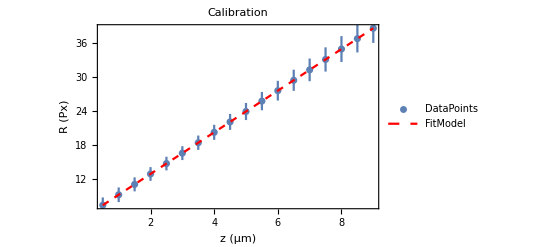

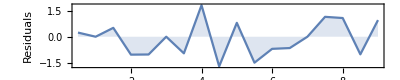

```mathematica
(*Print Results*)
Print[]
Print[Style["Statistical Parameters",Underlined]]
Print["R^2 = ", SetPrecision[zRFit["RSquared"],4]]
Print["ν = ", SetPrecision[ν,4]]
Print["χ_ν^2 = ", SetPrecision[χ2ν,4]]
Print["P(χ_ν^2;ν) = ", SetPrecision[P,4]]
Print["D = ", SetPrecision[d,4]]
Print[zRFit["ParameterTable"]]
Print[]
(*Fit Plot*)
zRMeanListσ=MapAt[ErrorBar,Transpose[{zRMeanList,σMeanList}],{All,2}];
plot=Show[
ErrorListPlot[zRMeanListσ,PlotLegends->{"DataPoints"}],
Plot[zRFit[x],{x,First@zList,Last@zList},PlotStyle->{Red,Dashed},PlotLegends->{"FitModel"}],
Frame->True,
FrameLabel->{"z (μm)","R (Px)"},
PlotLabel->"Calibration",
PlotRange->{{Min[First/@zRMeanList],Max[First/@zRMeanList]},{Min@DeleteCases[RMeanList,0.],Max@RMeanList}}]
(*Residuals Plot*)
ResPlot=ListLinePlot[Transpose[{First/@zRMeanList,zRFit["StandardizedResiduals"]}], 
AspectRatio->1/5,
Frame->True,
Filling->Axis,
FrameLabel->{"z (μm)","Residuals"},
PlotRange->{{Min[First/@zRMeanList],Max[First/@zRMeanList]},Automatic}]
```

```mathematica
(*Export Numerical Results & Plots*)
Export["ResultsPx/CalibrationPlot.pdf",plot];
Export["ResultsPx/Residuals.pdf",ResPlot];
Export["ResultsPx/R2.dat",SetPrecision[zRFit["RSquared"],4]];Export["ResultsPx/DoF.dat",SetPrecision[ν,4]];Export["ResultsPx/Chi2.dat",SetPrecision[χ2ν,4]];Export["ResultsPx/P.dat",SetPrecision[P,4]];
Export["ResultsPx/D.dat",SetPrecision[d,4]];
Export["ResultsPx/b.dat",SetPrecision[zRFit["BestFitParameters"][[1]],4]];
Export["ResultsPx/m.dat",SetPrecision[zRFit["BestFitParameters"][[2]],4]];
```